### Generate matches

Construction of the Steiner system S(2,4,28) based on from Theorem 2.3 of:
Reid C., Rosa A., “Steiner systems S(2, 4, v) — a survey,” Electronic Journal of Combinatorics (2010)
The system S(2,4,28) consists of a set V of 28 elements, and a set B of length-4 subsets of V such that that every length-2 subset of V appears in exactly one element of B.  In other words, V is a list of players, B is a list of four-player matches, and every player plays every other player at exactly once.  B, in this case, has 63 elements.

```mathematica
Needs["FiniteFields`"]
```

```mathematica
t=2;(*so far I've only implemented the case of v≡4 mod 12; this may not work for other values of t (≠2) since I haven't implemented the algorithm completely rigorously*)
v=12t+4;
pn=4t+1;(*p^n in the paper*)
ℱ=GF[pn];(*finite field of order p^n*)
X=Table[ReduceElement[FromElementCode[ℱ,i]],{i,0,pn-1}];(*elements in ℱ*)
Do[
If[Sort[Table[ReduceElement[a^n],{n,pn-1}]]==Sort[Rest[X]],
α=a;Break[]],
{a,X}];(*find a generator (a.k.a primitive root) α such that every nonzero element of ℱ is equal to α^i for some integer i*)
c=1;(*I guessed here, but it works.  I think any c such that α^c≠±1 will work, since then (α^c+1)/(α^c-1) is nonzero and there is no division by zero: therefore there exists some q such that (α^c+1)/(α^c-1)=α^q, by definition of α.  Since α cannot be 1 (1^i=1), then we just have to avoid -1, which should(?) be the last element considered, and there are usually (also ?) multiple generators*)
B=Flatten[Table[{
{{α^(2i)+j,1},{α^(2t+2i)+j,1},{α^(2i+c)+j,2},{α^(2t+2i+c)+j,2}},
{{α^(2i)+j,2},{α^(2t+2i)+j,2},{α^(2i+c)+j,3},{α^(2t+2i+c)+j,3}},
{{α^(2i)+j,3},{α^(2t+2i)+j,3},{α^(2i+c)+j,1},{α^(2t+2i+c)+j,1}},
{{∞},{j,1},{j,2},{j,3}}
},{i,0,t-1},{j,X}],2];(*find the base blocks and all of the cyclical permutations at the same time.  Note that ∞ is a fixed point*)
B=B/.{e:(_GF[___]):>ToElementCode[e]};(*convert field elements to numbers so that Union[] works later*)
V=Union[Flatten[B,1]];
B=B/.Thread[V->Range[v]];(*convert the elements of V to numbers for easy processing later*)
V=Range[v];
B=Union[Sort/@B](*eliminate duplicates*)
```

{{1,2,3,4},{1,5,6,7},{1,8,9,10},{1,11,12,13},{1,14,15,16},{1,17,18,19},{1,20,21,22},{1,23,24,25},{1,26,27,28},{2,5,18,27},{2,6,21,23},{2,7,13,14},{2,8,15,24},{2,9,12,17},{2,10,22,26},{2,11,25,28},{2,16,19,20},{3,5,11,15},{3,6,19,28},{3,7,22,24},{3,8,20,27},{3,9,16,25},{3,10,13,18},{3,12,23,26},{3,14,17,21},{4,5,20,25},{4,6,12,16},{4,7,17,26},{4,8,11,19},{4,9,21,28},{4,10,14,23},{4,13,24,27},{4,15,18,22},{5,8,12,21},{5,9,24,26},{5,10,16,17},{5,13,19,23},{5,14,22,28},{6,8,14,18},{6,9,13,22},{6,10,25,27},{6,11,17,24},{6,15,20,26},{7,8,23,28},{7,9,15,19},{7,10,11,20},{7,12,18,25},{7,16,21,27},{8,13,16,26},{8,17,22,25},{9,11,14,27},{9,18,20,23},{10,12,15,28},{10,19,21,24},{11,16,22,23},{11,18,21,26},{12,14,20,24},{12,19,22,27},{13,15,21,25},{13,17,20,28},{14,19,25,26},{15,17,23,27},{16,18,24,28}}

### Split matches into rounds

```mathematica
f[list_,remaining_]:=If[(*yay, a recursive algorithm!*)
remaining=={},(*base case, if there are not more pairs remaining, return the completed list*)
list,
Block[{return=None,next=First[remaining],rest=Rest[remaining]},
Do[(*loop over each round*)
If[Intersection[Flatten[list[[i]]],next]=={},(*if none of the teams in the next match are in the given round*)
return=f[MapAt[Append[#,next]&,list,i],rest];(*recurse, adding the next match to the given round*)
If[return===None,(*if return = None, that sucks: putting the next match in that round broke everything, continue with the chain*)
,
Break[];
]
],
{i,Length[list]}];
return](*if return ≠ None, the base case has been reached: pass it up the chain; otherwise you're stuck and you have to go up a level anyway*)
]
sets=f[ConstantArray[{},9],B](*initialize each of the 9 rounds to be empty*)
```

{{{1,2,3,4},{5,8,12,21},{6,9,13,22},{7,10,11,20},{14,19,25,26},{15,17,23,27},{16,18,24,28}},{{1,5,6,7},{2,8,15,24},{3,9,16,25},{4,10,14,23},{11,18,21,26},{12,19,22,27},{13,17,20,28}},{{1,8,9,10},{2,5,18,27},{3,6,19,28},{4,7,17,26},{11,16,22,23},{12,14,20,24},{13,15,21,25}},{{1,11,12,13},{2,16,19,20},{3,14,17,21},{4,15,18,22},{5,9,24,26},{6,10,25,27},{7,8,23,28}},{{1,14,15,16},{2,10,22,26},{3,8,20,27},{4,9,21,28},{5,13,19,23},{6,11,17,24},{7,12,18,25}},{{1,17,18,19},{2,6,21,23},{3,7,22,24},{4,5,20,25},{8,13,16,26},{9,11,14,27},{10,12,15,28}},{{1,20,21,22},{2,11,25,28},{3,12,23,26},{4,13,24,27},{5,10,16,17},{6,8,14,18},{7,9,15,19}},{{1,23,24,25},{2,9,12,17},{3,10,13,18},{4,8,11,19},{5,14,22,28},{6,15,20,26},{7,16,21,27}},{{1,26,27,28},{2,7,13,14},{3,5,11,15},{4,6,12,16},{8,17,22,25},{9,18,20,23},{10,19,21,24}}}

### Order matches/rounds

```mathematica
g[list_,remaining_,n_]:=If[
remaining=={},
list,
Block[{return=None},
Do[(*loop over each match in the current round*)
If[Intersection[Flatten[list[[-n;;]]],choice]=={},(*any of the teams in the selected match have not participated in the last n matches...*)
return=g[(*recurse!*)
Append[list,choice],(*add the current match to the sequence*)
If[
Length[First[remaining]]==1,(*if there is only one match remaining in the current round...*)
Rest[remaining],(*return all of the following rounds*)
Prepend[Rest[remaining],DeleteCases[First[remaining],choice]](*otherwise, delete the selected match from the round*)
],
n];
If[return===None,
,
Break[];(*if return ≠ None, break the loop and return*)
]
],
{choice,First[remaining]}];
return](*the structure is pretty much the same as the previous recursive function*)
]
best={};(*initialize the counter*)
Dynamic[best]
n=0;
Do[(*for every ordering (permutation) of the rounds:*)
While[True,
current=g[First[s],Rest[s],n];(*calculate an ordering with the previous best spacing+1*)
If[current===None,(*if it failed...*)
Break[],(*break out of the while-loop, continue to the next permutation*)
best=current(*otherwise we have a new best ordering*)
];
n++(*increase the spacing by one for the next ordering*)
],
{s,Permutations[sets]}];(*I don't know if the loop actually helps, but it only takes like 30 seconds*)
ordering=best/.Thread[Take[Flatten[best],v]->V];(*use an isomporphism to map the result onto itself with a specified ordering*)
```

### Visualization

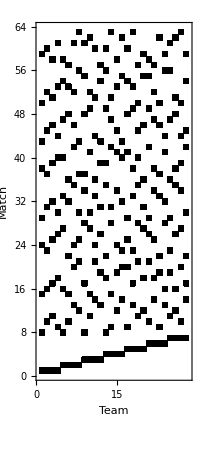

Round 1, match 1: Teams  1,  2,  3, and  4
Round 1, match 2: Teams  5,  6,  7, and  8
Round 1, match 3: Teams  9, 10, 11, and 12
Round 1, match 4: Teams 13, 14, 15, and 16
Round 1, match 5: Teams 17, 18, 19, and 20
Round 1, match 6: Teams 21, 22, 23, and 24
Round 1, match 7: Teams 25, 26, 27, and 28
Round 2, match 1: Teams  1,  5,  9, and 13
Round 2, match 2: Teams  4, 14, 17, and 23
Round 2, match 3: Teams  2,  6, 21, and 27
Round 2, match 4: Teams  3, 10, 25, and 19
Round 2, match 5: Teams 15, 26,  8, and 20
Round 2, match 6: Teams  7, 18, 12, and 24
Round 2, match 7: Teams 11, 22, 16, and 28
Round 3, match 1: Teams  1,  6, 10, and 14
Round 3, match 2: Teams  2,  5, 26, and 24
Round 3, match 3: Teams  3,  9, 18, and 28
Round 3, match 4: Teams  4, 13, 22, and 20
Round 3, match 5: Teams 15, 25, 12, and 23
Round 3, match 6: Teams  7, 17, 16, and 27
Round 3, match 7: Teams 11, 21,  8, and 19
Round 4, match 1: Teams 13,  6, 23, and 28
Round 4, match 2: Teams  2, 25, 18, and 16
Round 4, match 3: Teams  1, 15,  7, and 11
Round 4, match 4: Teams  3, 17, 22, and  8
Round 4, match 5: Teams  4, 21, 26, and 12
Round 4, match 6: Teams  5, 10, 27, and 20
Round 4, match 7: Teams  9, 14, 19, and 24
Round 5, match 1: Teams  1, 17, 21, and 25
Round 5, match 2: Teams  4, 10,  8, and 28
Round 5, match 3: Teams  2, 14, 12, and 20
Round 5, match 4: Teams  3,  6, 16, and 24
Round 5, match 5: Teams  5, 11, 18, and 23
Round 5, match 6: Teams  9, 15, 22, and 27
Round 5, match 7: Teams 13,  7, 26, and 19
Round 6, match 1: Teams  6, 11, 25, and 20
Round 6, match 2: Teams  2,  9,  8, and 23
Round 6, match 3: Teams  1, 22, 26, and 18
Round 6, match 4: Teams  3, 13, 12, and 27
Round 6, match 5: Teams  4,  5, 16, and 19
Round 6, match 6: Teams 10, 15, 17, and 24
Round 6, match 7: Teams 14,  7, 21, and 28
Round 7, match 1: Teams  1, 16,  8, and 12
Round 7, match 2: Teams  4, 11, 27, and 24
Round 7, match 3: Teams  2, 15, 19, and 28
Round 7, match 4: Teams  3,  7, 23, and 20
Round 7, match 5: Teams  5, 14, 25, and 22
Round 7, match 6: Teams  9,  6, 17, and 26
Round 7, match 7: Teams 13, 10, 21, and 18
Round 8, match 1: Teams  1, 23, 27, and 19
Round 8, match 2: Teams  3, 14, 11, and 26
Round 8, match 3: Teams  2, 10,  7, and 22
Round 8, match 4: Teams  4,  6, 15, and 18
Round 8, match 5: Teams  5, 17, 12, and 28
Round 8, match 6: Teams  9, 21, 16, and 20
Round 8, match 7: Teams 13, 25,  8, and 24
Round 9, match 1: Teams  6, 22, 12, and 19
Round 9, match 2: Teams  3,  5, 15, and 21
Round 9, match 3: Teams  1, 20, 24, and 28
Round 9, match 4: Teams  2, 13, 11, and 17
Round 9, match 5: Teams  4,  9,  7, and 25
Round 9, match 6: Teams 10, 26, 16, and 23
Round 9, match 7: Teams 14, 18,  8, and 27

Team  1: round 1, match 1; round 2, match 1; round 3, match 1; round 4, match 3; round 5, match 1; round 6, match 3; round 7, match 1; round 8, match 1; and round 9, match 3
Team  2: round 1, match 1; round 2, match 3; round 3, match 2; round 4, match 2; round 5, match 3; round 6, match 2; round 7, match 3; round 8, match 3; and round 9, match 4
Team  3: round 1, match 1; round 2, match 4; round 3, match 3; round 4, match 4; round 5, match 4; round 6, match 4; round 7, match 4; round 8, match 2; and round 9, match 2
Team  4: round 1, match 1; round 2, match 2; round 3, match 4; round 4, match 5; round 5, match 2; round 6, match 5; round 7, match 2; round 8, match 4; and round 9, match 5
Team  5: round 1, match 2; round 2, match 1; round 3, match 2; round 4, match 6; round 5, match 5; round 6, match 5; round 7, match 5; round 8, match 5; and round 9, match 2
Team  6: round 1, match 2; round 2, match 3; round 3, match 1; round 4, match 1; round 5, match 4; round 6, match 1; round 7, match 6; round 8, match 4; and round 9, match 1
Team  7: round 1, match 2; round 2, match 6; round 3, match 6; round 4, match 3; round 5, match 7; round 6, match 7; round 7, match 4; round 8, match 3; and round 9, match 5
Team  8: round 1, match 2; round 2, match 5; round 3, match 7; round 4, match 4; round 5, match 2; round 6, match 2; round 7, match 1; round 8, match 7; and round 9, match 7
Team  9: round 1, match 3; round 2, match 1; round 3, match 3; round 4, match 7; round 5, match 6; round 6, match 2; round 7, match 6; round 8, match 6; and round 9, match 5
Team 10: round 1, match 3; round 2, match 4; round 3, match 1; round 4, match 6; round 5, match 2; round 6, match 6; round 7, match 7; round 8, match 3; and round 9, match 6
Team 11: round 1, match 3; round 2, match 7; round 3, match 7; round 4, match 3; round 5, match 5; round 6, match 1; round 7, match 2; round 8, match 2; and round 9, match 4
Team 12: round 1, match 3; round 2, match 6; round 3, match 5; round 4, match 5; round 5, match 3; round 6, match 4; round 7, match 1; round 8, match 5; and round 9, match 1
Team 13: round 1, match 4; round 2, match 1; round 3, match 4; round 4, match 1; round 5, match 7; round 6, match 4; round 7, match 7; round 8, match 7; and round 9, match 4
Team 14: round 1, match 4; round 2, match 2; round 3, match 1; round 4, match 7; round 5, match 3; round 6, match 7; round 7, match 5; round 8, match 2; and round 9, match 7
Team 15: round 1, match 4; round 2, match 5; round 3, match 5; round 4, match 3; round 5, match 6; round 6, match 6; round 7, match 3; round 8, match 4; and round 9, match 2
Team 16: round 1, match 4; round 2, match 7; round 3, match 6; round 4, match 2; round 5, match 4; round 6, match 5; round 7, match 1; round 8, match 6; and round 9, match 6
Team 17: round 1, match 5; round 2, match 2; round 3, match 6; round 4, match 4; round 5, match 1; round 6, match 6; round 7, match 6; round 8, match 5; and round 9, match 4
Team 18: round 1, match 5; round 2, match 6; round 3, match 3; round 4, match 2; round 5, match 5; round 6, match 3; round 7, match 7; round 8, match 4; and round 9, match 7
Team 19: round 1, match 5; round 2, match 4; round 3, match 7; round 4, match 7; round 5, match 7; round 6, match 5; round 7, match 3; round 8, match 1; and round 9, match 1
Team 20: round 1, match 5; round 2, match 5; round 3, match 4; round 4, match 6; round 5, match 3; round 6, match 1; round 7, match 4; round 8, match 6; and round 9, match 3
Team 21: round 1, match 6; round 2, match 3; round 3, match 7; round 4, match 5; round 5, match 1; round 6, match 7; round 7, match 7; round 8, match 6; and round 9, match 2
Team 22: round 1, match 6; round 2, match 7; round 3, match 4; round 4, match 4; round 5, match 6; round 6, match 3; round 7, match 5; round 8, match 3; and round 9, match 1
Team 23: round 1, match 6; round 2, match 2; round 3, match 5; round 4, match 1; round 5, match 5; round 6, match 2; round 7, match 4; round 8, match 1; and round 9, match 6
Team 24: round 1, match 6; round 2, match 6; round 3, match 2; round 4, match 7; round 5, match 4; round 6, match 6; round 7, match 2; round 8, match 7; and round 9, match 3
Team 25: round 1, match 7; round 2, match 4; round 3, match 5; round 4, match 2; round 5, match 1; round 6, match 1; round 7, match 5; round 8, match 7; and round 9, match 5
Team 26: round 1, match 7; round 2, match 5; round 3, match 2; round 4, match 5; round 5, match 7; round 6, match 3; round 7, match 6; round 8, match 2; and round 9, match 6
Team 27: round 1, match 7; round 2, match 3; round 3, match 6; round 4, match 6; round 5, match 6; round 6, match 4; round 7, match 2; round 8, match 1; and round 9, match 7
Team 28: round 1, match 7; round 2, match 7; round 3, match 3; round 4, match 1; round 5, match 2; round 6, match 7; round 7, match 3; round 8, match 5; and round 9, match 3

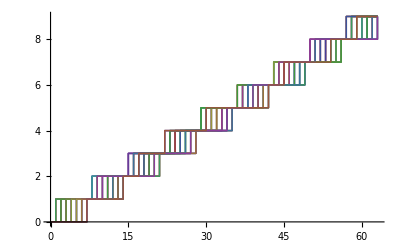

```mathematica
positions=(Flatten/@Flatten[MapIndexed[List,ordering,{2}],1])[[;;,;;2]];
(*draw a sort of schedule diagram thingey*)
Graphics[Rectangle/@(positions-1/2),GridLines->{Range,Range},PlotRange->{{0,28}+1/2,{0,63}+1/2},Frame->True,FrameLabel->{"Team","Match"}]
(*schedule: which teams play in a given match*)
Column[MapIndexed[Row[Flatten[{"Round ",Ceiling[First[#2]/7],", match ",Mod[First[#2],7,1],": Teams ",Insert[Riffle[PaddedForm[#,2,NumberSigns->{"",""}]&/@#1,", "],"and ",-2]}]]&,ordering]]
(*itinerary: which matches a given team plays*)
Column[MapIndexed[Row[Flatten[{"Team ",PaddedForm[First[#2],2,NumberSigns->{"",""}],": ",Insert[Riffle[{"round ",Ceiling[#/7],", match ",Mod[#,7,1]}&/@#1,"; "],"and ",-2]}]]&,SplitBy[Sort[positions],First][[;;,;;,2]]]]
(*graph the number of matches per team over time; shows that no team has more than one more match played than any other team*)
ListLinePlot[Transpose[{Flatten@Partition[Prepend[Append[Last/@#,Length[ordering]],0],2,1],Floor@Range[0,Length[#]+1/2,1/2]}]&/@SplitBy[Sort[positions],First]]
```